```mathematica
n=5
L = Function[{mu,S},(1/(√(2 π S S)))^n ⅇ^(-(0.01009121-mu)^2/(2 S S))ⅇ^(-(3.63415088-mu)^2/(2 S S))ⅇ^(-(-1.40851589-mu)^2/(2 S S))ⅇ^(-(3.70573177-mu)^2/(2 S S))ⅇ^(-(-0.94145782-mu)^2/(2 S S))]
lnL = Function[{mu,S}, Log[L[mu, S]]]
sHat =Function[mu, (((0.0100912-mu)^2+(3.63415-mu)^2+(-1.40852-mu)^2+(3.70573-mu)^2+(-0.941458-mu)^2)/n)^.5]
```

5

Function[{mu,S},(1/(√(2 π S S)))^n ⅇ^(-(0.0100912-mu)^2/(2 S S)) ⅇ^(-(3.63415-mu)^2/(2 S S)) ⅇ^(-(-1.40852-mu)^2/(2 S S)) ⅇ^(-(3.70573-mu)^2/(2 S S)) ⅇ^(-(-0.941458-mu)^2/(2 S S))]

Function[{mu,S},Log[L[mu,S]]]

Function[mu,(((0.0100912-mu)^2+(3.63415-mu)^2+(-1.40852-mu)^2+(3.70573-mu)^2+(-0.941458-mu)^2)/n)^0.5]

```mathematica
5Log[1/√(2 π)] - (0.9799194+ 6.9387509+5.8009488+7.3209844+3.7692585)/2
```

-16.9996

```mathematica
sHat[0]
```

2.44171

```mathematica
,
```

Function[{mu,S},(1/5 ((0.0100912-mu)^2+(3.63415-mu)^2+(-1.40852-mu)^2+(3.70573-mu)^2+(-0.941458-mu)^2))^0.5]

```mathematica
lnL[0,1] 
lnL[1,1]
lnL[0,sHat[0]]
lnL[1, sHat[1]]
lnL[0,1] - lnL[1,1]
lnL[0,sHat[0]] - lnL[1, sHat[1]]
lnL[0,sHat[1]]
```

-19.4996

-16.9996

-11.5582

-11.0992

-2.5

-0.458995

-11.603

```mathematica
sHat[0]
sHat[1]
```

2.44171

2.22755

```mathematica
2.2275487982929327
lnL[1,1] -1.92
```

2.22755

-18.9196

```mathematica
NSolve[{lnL[mu,1] + 1.92 == lnL[1,1]},{mu}]
```

{{mu→0.123644},{mu→1.87636}}

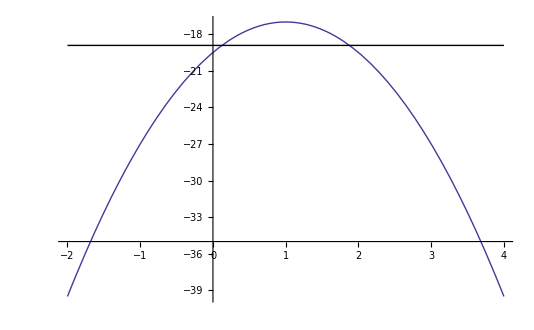

```mathematica
Plot[{lnL[mu,1], lnL[1,1] -1.92}, {mu,-2,4} ,PlotStyle->{{Thick}, {Black, Thick}}]
```

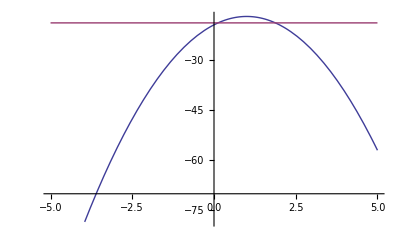

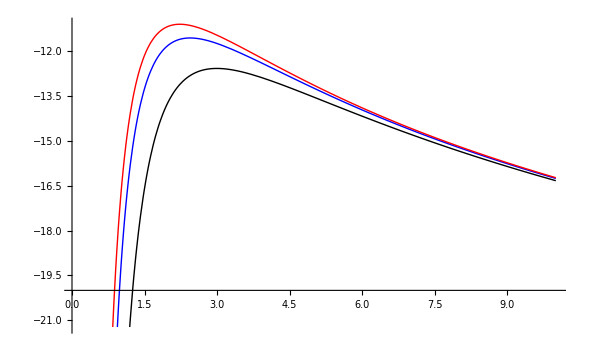

```mathematica
Plot[{lnL[-1, S], lnL[0,S], lnL[1,S]}, {S,0.05, 10}, PlotStyle->{{Black,Thick}, {Blue,Thick},{Red,Thick}}]
```

-11.0992

-410.749

399.649

-13.0192

-14.0949

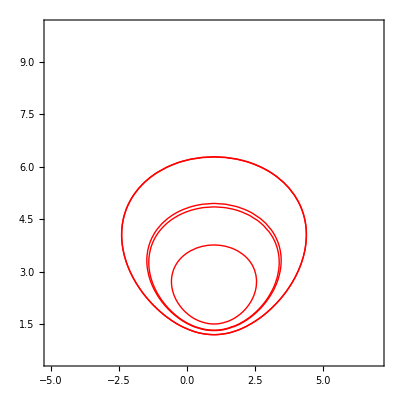

```mathematica
ref = lnL[1, sHat[1]]
lowest = lnL[-5,0.5]
denom = ref-lowest
x=ref - 1.92
y = ref - (5.9914/2)
ContourPlot[{lnL[mu, S] == ref - 1,
		      lnL[mu, S] == x, 
                        lnL[mu, S] == ref - 2,
		      lnL[mu,S]==y,
			lnL[mu, S] == ref - 3
		      }, {mu,-5,7}, {S,0.5, 10}, ColorFunction->(If[#1 > x,Red,White] &),PlotRange->{lowest,ref}]
```

```mathematica
Plot3D[{lnL[mu, S]}, {mu,-4,6}, {S,0.5, 8}, PlotStyle->{{},{Red,Opacity[.9], Thick},{Blue,Opacity[.5], Thick}}, ViewPoint->Top]
Plot3D[{lnL[mu, S], lnL[1, sHat[1]] - 1.92}, {mu,-4,6}, {S,0.5, 8}, PlotStyle->{{},{Red,Opacity[.9], Thick},{Blue,Opacity[.5], Thick}}, ViewPoint->Top]
Plot3D[{lnL[mu, S], lnL[1, sHat[1]] - 2.995732}, {mu,-4,6}, {S,0.5, 8}, PlotStyle->{{},{Red,Opacity[.9], Thick},{Blue,Opacity[.5], Thick}}, ViewPoint->Top]
Plot3D[{lnL[mu, S], lnL[1, sHat[1]] - 2.995732,lnL[1, sHat[1]] - 1.92}, {mu,-4,6}, {S,0.5, 8}, PlotStyle->{{},{Red,Opacity[.9], Thick},{Blue,Opacity[.5], Thick}}, ViewPoint->Top]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Plot3D[{lnL[mu, S]}, {mu,-4,6}, {S,0.5, 8}, PlotStyle->{{},{Purple,Opacity[.6], Thick}}, ViewPoint->Top]
```

-Graphics3D-

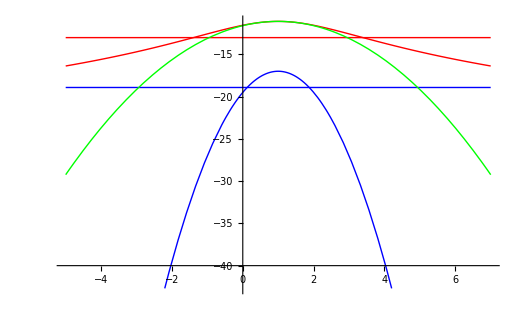

```mathematica
Plot[{lnL[mu,1], lnL[mu, sHat[mu]], lnL[1,sHat[1]] -1.92, lnL[1,1] -1.92, lnL[mu, sHat[1]]}, {mu,-5,7}, PlotStyle->{{Blue, Thick},{Red, Thick}, {Red}, {Blue}, {Green, Thick}}]
```

```mathematica
Ciel = Function[{mu, S}, If [S ≥ sHat[mu], lnL[mu, sHat[mu]],-40]];Plot3D[{lnL[mu, S], Ciel[mu,S]}, {mu,-4,6}, {S,0.5, 8}, PlotStyle->{{},{Red,Opacity[.9], Thick},{Blue,Opacity[.5], Thick}}, ViewPoint->Top]
```

-Graphics3D-

-Graphics3D-

1

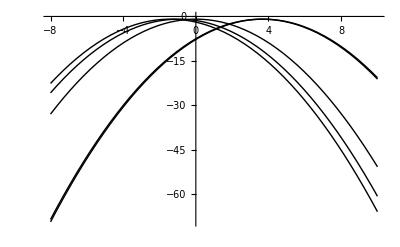

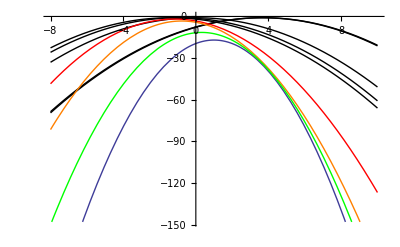

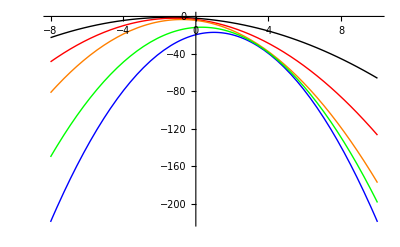

```mathematica
sd = 1
Plot[{Log[(1/(√(2 π sd sd)))]-(0.01009121-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(3.63415088-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(3.70573177-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(-0.94145782-mu)^2/(2 sd sd )} , {mu,-8,10} ,PlotStyle->{{Black}, {Black}, {Black}, {Black}, {Black}}]
Plot[{lnL[mu,sd], Log[(1/(√(2 π sd sd)))]-(0.01009121-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(3.63415088-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(3.70573177-mu)^2/(2 sd sd ),Log[(1/(√(2 π sd sd)))]-(-0.94145782-mu)^2/(2 sd sd ), 2 Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ) -(-0.94145782-mu)^2/(2 sd sd ), 3 Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ) -(-0.94145782-mu)^2/(2 sd sd ) -(0.01009121-mu)^2/(2 sd sd ), 
4 Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ) -(-0.94145782-mu)^2/(2 sd sd ) -(0.01009121-mu)^2/(2 sd sd )-(3.63415088-mu)^2/(2 sd sd )} , {mu,-8,10} ,PlotStyle->{{Thick}, {Black}, {Black}, {Black,Thick}, {Black}, {Black}, {Red,Thick},{Orange,Thick},{Green,Thick}}]
Plot[{lnL[mu,sd], Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ), 2 Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ) -(-0.94145782-mu)^2/(2 sd sd ), 3 Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ) -(-0.94145782-mu)^2/(2 sd sd ) -(0.01009121-mu)^2/(2 sd sd ), 
4 Log[(1/(√(2 π sd sd)))]-(-1.40851589-mu)^2/(2 sd sd ) -(-0.94145782-mu)^2/(2 sd sd ) -(0.01009121-mu)^2/(2 sd sd )-(3.63415088-mu)^2/(2 sd sd )} , {mu,-8,10} ,PlotStyle->{{Blue, Thick}, {Black,Thick}, {Red,Thick},{Orange,Thick},{Green,Thick}}]
```